## Notebook for Homework 1

#### Get the Data

This is the location of the data on an Excel file:

```mathematica
originalFile="/Users/jaimebuitrago/Dropbox/Jaime/Wolfram Summer School/Boston2017Hourly.xlsx";
```

```mathematica
(*originalFile2 = "/Users/jaimebuitrago/Dropbox/Jaime/Wolfram Summer School/EnergyJuneMA.xlsx"*)
```

We need to import the data into a variable and then cleanup

```mathematica
sheet=First@Import[originalFile]
```

```mathematica
headers=First@sheet
```

{DateHour,Actual}

```mathematica
data=Map[AssociationThread[headers->#]&,Rest@sheet]
```

{<|DateHour→Sun 1 Jan 2017 00:00:00GMT-4.,Actual→1542.56|>,<|DateHour→Sun 1 Jan 2017 01:00:00GMT-4.,Actual→1436.88|>,8756,<|DateHour→Sun 31 Dec 2017 21:59:59GMT-4.,Actual→1769.91|>}
 |  |  |  |

```mathematica
data1=Rule@@@data[[All,{"DateHour","Actual"}]]
```

{Sun 1 Jan 2017 00:00:00GMT-4.→1542.56,Sun 1 Jan 2017 01:00:00GMT-4.→1436.88,Sun 1 Jan 2017 02:00:00GMT-4.→1401.3,8754,Sun 31 Dec 2017 20:59:59GMT-4.→2178.72,Sun 31 Dec 2017 21:59:59GMT-4.→1769.91}
 |  |  |  |

I want to use the first 11 months of the year for training, therefore I have to cut the dataset to only the first 11 months = 8016 hours

```mathematica
trainingset=data1[[1;;8017]];
```

```mathematica
validationset = data1[[-31*24+2;; ]];
```

```mathematica
dates= trainingset[[All,1]];
values = trainingset[[All,2]];
ts=TimeSeries[values,{dates}]
```

TimeSeries[…]

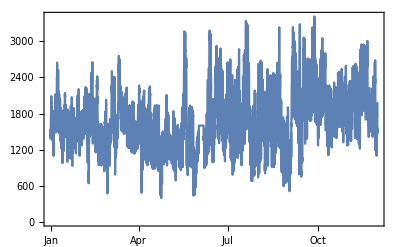

```mathematica
DateListPlot[ts]
```

```mathematica
dates1=validationset[[;;24,1]];
```

```mathematica
values1=validationset[[;;24,2]];
```

```mathematica
ts1=TimeSeries[values1,{dates1}]
```

TimeSeries[…]

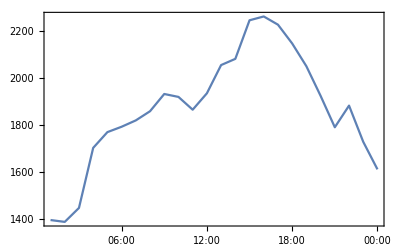

```mathematica
DateListPlot[ts1]
```

```mathematica
forecast=TimeSeriesForecast[ARProcess[{-.2,.4,.6},.1],values,2]
```

1263.09

```mathematica
tsm=TimeSeriesModelFit[ts]
```

TemporalData::rsmplng: The data is not uniformly spaced and will be automatically resampled to the resolution of the minimum time increment.

General::munfl: Exp[-3751.63] is too small to represent as a normalized machine number; precision may be lost.

TimeSeriesModel[…]

```mathematica
Normal[tsm]
```

ARMAProcess[148.581,{0.914609},{0.319144,0.296721,0.26723,0.209693,0.152596,0.0649568},12727.3]

```mathematica
z=tsm[Part[dates1,24]]
```

1692.93

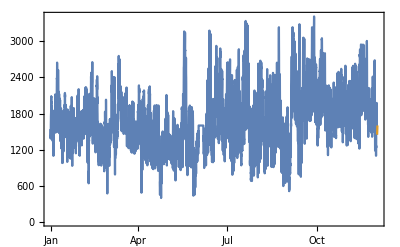

```mathematica
DateListPlot[{tsm["TemporalData"],TimeSeriesForecast[tsm,{12}]}]
```

```mathematica
ts[{October 1, 2017},{October 31, 2017}]
```

TimeSeries[…][{October,2017},{31 October,2017}]